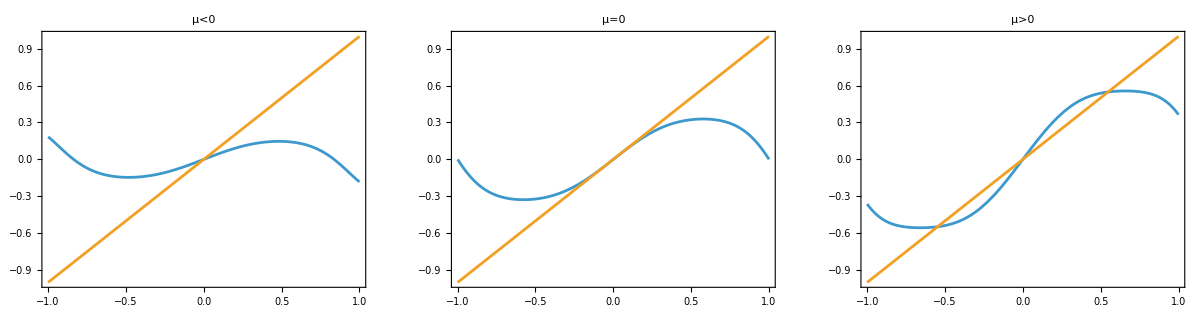

```mathematica
f[x_,μ_]:=-(1+μ)x+x^3;
f2[x_,μ_]:=f[f[x,μ],μ];
GraphicsGrid[{{Plot[{f2[x,-0.3],x},{x,-1,1},Frame->True,AspectRatio->0.8,PlotLabel->"μ<0"],
Plot[{f2[x,0],x},{x,-1,1},Frame->True,AspectRatio->0.8,PlotLabel->"μ=0"],
Plot[{f2[x,0.3],x},{x,-1,1},Frame->True,AspectRatio->0.8,PlotLabel->"μ>0"]}}]
```

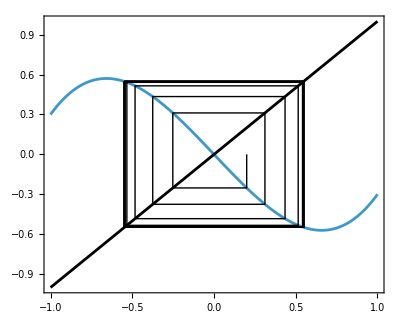

```mathematica
f[x_,μ_]:=-(1+μ)x+x^3;
μ=0.3;
g[{{a_,b_},{c_,d_},{e_,m_}}]:={{e,m},{m,f[m,μ]},{f[m,μ],f[m,μ]}};
range={x,-1,1};
n=30;
x0=0.2;
data=NestList[g,{{x0,0},{x0,f[x0,μ]},{f[x0,μ],f[x0,μ]}},n];
Show[Plot[f[x,μ],range],Plot[x,range,PlotStyle->Black],Graphics[Line/@data],AspectRatio->0.8,PlotRange->All,Frame->True]
```